## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.3, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL03=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.3)
```

0.299871

```mathematica
Zprime10decayfixedmass03[CvR_]:=MassZprime10/(12π)(1/4(CvL03+CvR)^2+1/4(CvL03-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL03+CvR)^2-1/2(CvL03+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass03Table=Table[{Q[i],Zprime10decayfixedmass03[Q[i]]},{i,0,Npt}]
```

{{0.,11.9228},{0.1,13.2479},{0.2,17.2248},{0.3,23.8534},{0.4,33.1339},{0.5,45.0661},{0.6,59.6502},{0.7,76.886},{0.8,96.7736},{0.9,119.313},{1.,144.504}}

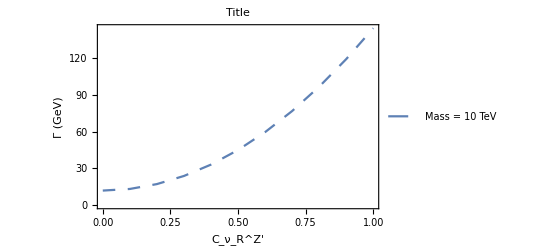

```mathematica
PlotZprimeDecayFixed1003=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

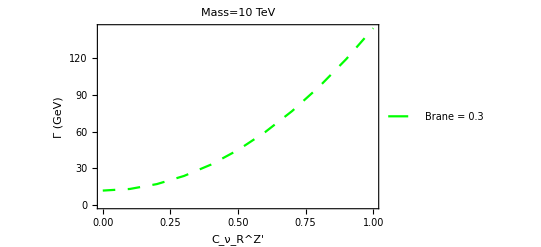

```mathematica
PlotZprimeDecayFixed1003B=ListPlot[%%, Joined-> True,PlotStyle->{Green,Dashing[Medium]},PlotLegends->{"Brane = 0.3"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass03Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 11.9228
0.1 | 13.2479
0.2 | 17.2248
0.3 | 23.8534
0.4 | 33.1339
0.5 | 45.0661
0.6 | 59.6502
0.7 | 76.886
0.8 | 96.7736
0.9 | 119.313
1. | 144.504

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.3, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL03=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.3)
```

0.299871

```mathematica
Zprime8decayfixedmass03[CvR_]:=MassZprime8/(12π)(1/4(CvL03+CvR)^2+1/4(CvL03-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL03+CvR)^2-1/2(CvL03+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass03Table=Table[{Q[i],Zprime8decayfixedmass03[Q[i]]},{i,0,Npt}]
```

{{0.,9.53662},{0.1,10.5962},{0.2,13.7768},{0.3,19.0785},{0.4,26.5012},{0.5,36.045},{0.6,47.7099},{0.7,61.4959},{0.8,77.4029},{0.9,95.4311},{1.,115.58}}

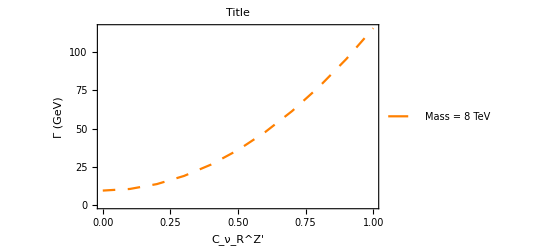

```mathematica
PlotZprimeDecayFixed803=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

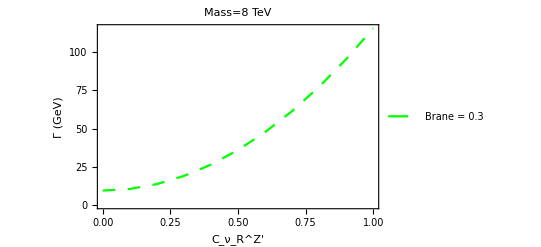

```mathematica
PlotZprimeDecayFixed803B=ListPlot[%%, Joined-> True,PlotStyle->{Green,Dashing[Medium]},PlotLegends->{"Brane = 0.3"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass03Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 9.53662
0.1 | 10.5962
0.2 | 13.7768
0.3 | 19.0785
0.4 | 26.5012
0.5 | 36.045
0.6 | 47.7099
0.7 | 61.4959
0.8 | 77.4029
0.9 | 95.4311
1. | 115.58

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.3, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL03=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.3)
```

0.299871

```mathematica
Zprime5decayfixedmass03[CvR_]:=MassZprime5/(12π)(1/4(CvL03+CvR)^2+1/4(CvL03-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL03+CvR)^2-1/2(CvL03+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass03Table=Table[{Q[i],Zprime5decayfixedmass03[Q[i]]},{i,0,Npt}]
```

{{0.,5.95602},{0.1,6.61678},{0.2,8.60224},{0.3,11.9124},{0.4,16.5473},{0.5,22.5068},{0.6,29.7911},{0.7,38.4},{0.8,48.3337},{0.9,59.5921},{1.,72.1751}}

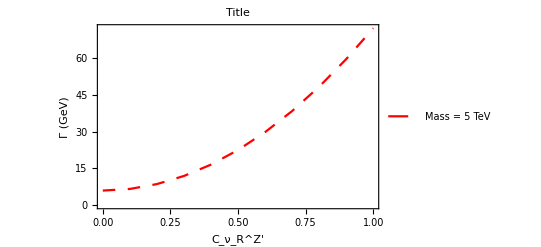

```mathematica
PlotZprimeDecayFixed503=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

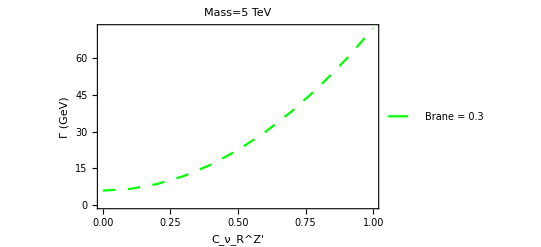

```mathematica
PlotZprimeDecayFixed503B=ListPlot[%%, Joined-> True,PlotStyle->{Green,Dashing[Medium]},PlotLegends->{"Brane = 0.3"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass03Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 5.95602
0.1 | 6.61678
0.2 | 8.60224
0.3 | 11.9124
0.4 | 16.5473
0.5 | 22.5068
0.6 | 29.7911
0.7 | 38.4
0.8 | 48.3337
0.9 | 59.5921
1. | 72.1751

## OverLay

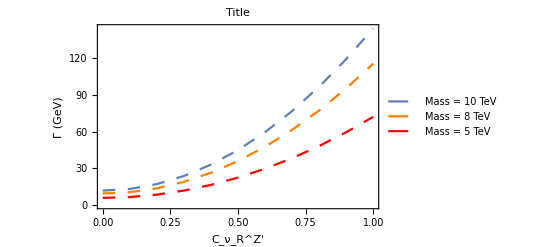

```mathematica
Show[PlotZprimeDecayFixed1003,PlotZprimeDecayFixed803,PlotZprimeDecayFixed503]
```

## OverLay 2

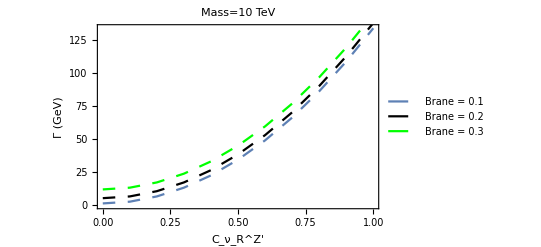

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B]
```

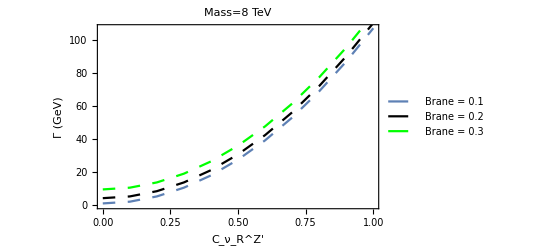

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B]
```

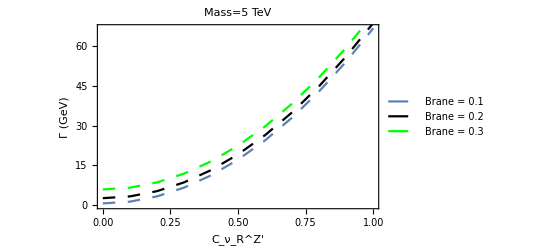

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B]
```